# Examples treated by Chris Trana

### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Test 2

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs02=FromReducedRankIndex[2]
```

<|Index→2,QCode→0,RuleSet→{A→,→A}|>

We generate the sessie and its causal network, again giving it a convenient name:

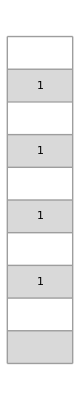
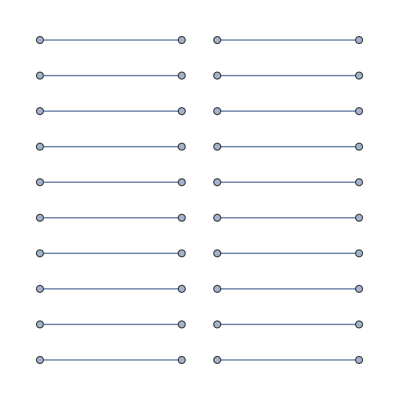
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss02=SSS[rs02[["RuleSet"]], "",40, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->10, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss02[["Net"]]
```

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30,31→32,33→34,35→36,37→38,39→40}

```mathematica
nds02=ToNetDifferenceSets[sss02[["Net"]]]
```

{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

Try the reduction:

```mathematica
rsl02=ReduceSetList[nds02]
```

{€^19[{1},{}],{1}}

Look for a most compressed part.

Get an editable version of that last complete line:

```mathematica
rsl02[[1]]
```

€^19[{1},{}]

```mathematica
rsl02[[]]//InputForm
```

{IndexedConcatenate[{1}, {}, 19], {1}}

### Bottom Line:

RuleSet & IC form:

```mathematica
<|"Index"->2,"QCode"->"0","RuleSet"->{"A"->"",""->"A"}|>
```

```mathematica
rsl02[[1]]//InputForm
```

IndexedConcatenate[{1}, {}, 19]

```mathematica
IndexedConcatenate[{1}, {}, ∞]
```

€^∞[{1},{}]

### Chris Trana’s Summary

∪_(n=1)^∞{2n-1->2n}

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30,31→32,33→34,35→36,37→38,39→40}

How to get from here to there?

```mathematica
IndexedConcatenate[{1}, {}, {n,1,∞}]
```

€_(n⊨1)^∞[{1},{}]

We have to use the length of the subsequence in the IC: 2, and the 1:

∪_(n=1)^∞{2n-1->(2n-1)+1}

### Test 4

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs04=FromReducedRankIndex[4]
```

<|Index→4,QCode→2,RuleSet→{A→A}|>

We generate the sessie and its causal network, again giving it a convenient name:

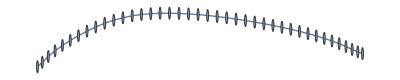
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
sss04=SSS[rs04[["RuleSet"]], "A",40, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->10, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->400,SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss04[["Net"]]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→21,21→22,22→23,23→24,24→25,25→26,26→27,27→28,28→29,29→30,30→31,31→32,32→33,33→34,34→35,35→36,36→37,37→38,38→39,39→40}

```mathematica
nds04=ToNetDifferenceSets[sss04[["Net"]]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

Try the reduction:

```mathematica
rsl04=ReduceSetList[nds04]
```

{€^39[{1}]}

```mathematica
rsl04//InputForm
```

{IndexedConcatenate[{1}, 39]}

### Bottom Line:

RuleSet & IC form:

```mathematica
<|"Index"->4,"QCode"->"2","RuleSet"->{"A"->"A"}|>
```

```mathematica
rsl04//InputForm
```

```mathematica
{IndexedConcatenate[{1}, ∞]}
```

{€^∞[{1}]}

### Chris Trana’s Summary

∪_(n=1)^∞{n->n+1}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→21,21→22,22→23,23→24,24→25,25→26,26→27,27→28,28→29,29→30,30→31,31→32,32→33,33→34,34→35,35→36,36→37,37→38,38→39,39→40}

Again, using the length of the subsequence in the IC: 1, and the 1:

∪_(n=1)^∞{1n->1n+1}

### Test 888

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs888=FromReducedRankRuleSet[{"BA"->"AB","AB"->"AC","AC"->"CA","CA"->"BA"}]
```

<|Index→8883014856242566230,QCode→432342342344234424432443243,RuleSet→{BA→AB,AB→AC,AC→CA,CA→BA}|>

We generate the sessie and its causal network, again giving it a convenient name:

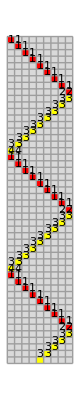


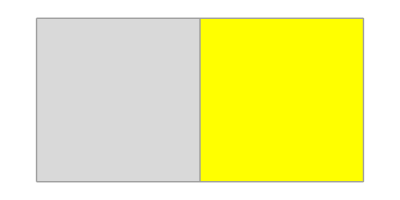
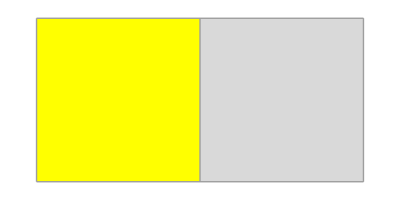
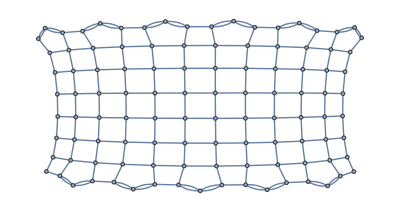
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss888=SSS[rs888[["RuleSet"]], "BAAAAAAAA",107, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->50, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->400,SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss888[["Net"]]//Short
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,«192»,93→105,104→105,92→106,105→106,91→107,106→107}

```mathematica
nds888=ToNetDifferenceSets[sss888[["Net"]]]
```

{{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1},{1},{1},{1},{1},{1},{1}}

Try the reduction:

```mathematica
rsl888=ReduceSetList[nds888]
```

{€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

```mathematica
rsl888[[1]]
```

€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]]

```mathematica
InputForm[rsl888[[1]]]
```

IndexedConcatenate[{1, 16}, {1, 14}, {1, 12}, {1, 10}, {1, 8}, {1, 6}, {1, 4}, 
 IndexedConcatenate[{1, 1}, 2], 11]

### Bottom Line:

RuleSet & IC form:

<|Index→8883014856242566230,QCode→432342342344234424432443243,RuleSet→{BA→AB,AB→AC,AC→CA,CA→BA}|>

```mathematica
IndexedConcatenate[{1, 16}, {1, 14}, {1, 12}, {1, 10}, {1, 8}, {1, 6}, {1, 4}, 
 IndexedConcatenate[{1, 1}, 2], ∞]
```

€^∞[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]]

### Chris Trana’s Summary

∪_(n=0)^∞{...}:

```mathematica
sss888[["Net"]]//Sort
```

{1→2,1→17,2→3,2→16,3→4,3→15,4→5,4→14,5→6,5→13,6→7,6→12,7→8,7→11,8→9,8→9,9→10,9→10,10→11,10→26,11→12,11→25,12→13,12→24,13→14,13→23,14→15,14→22,15→16,15→21,16→17,16→20,17→18,17→18,18→19,18→19,19→20,19→35,20→21,20→34,21→22,21→33,22→23,22→32,23→24,23→31,24→25,24→30,25→26,25→29,26→27,26→27,27→28,27→28,28→29,28→44,29→30,29→43,30→31,30→42,31→32,31→41,32→33,32→40,33→34,33→39,34→35,34→38,35→36,35→36,36→37,36→37,37→38,37→53,38→39,38→52,39→40,39→51,40→41,40→50,41→42,41→49,42→43,42→48,43→44,43→47,44→45,44→45,45→46,45→46,46→47,46→62,47→48,47→61,48→49,48→60,49→50,49→59,50→51,50→58,51→52,51→57,52→53,52→56,53→54,53→54,54→55,54→55,55→56,55→71,56→57,56→70,57→58,57→69,58→59,58→68,59→60,59→67,60→61,60→66,61→62,61→65,62→63,62→63,63→64,63→64,64→65,64→80,65→66,65→79,66→67,66→78,67→68,67→77,68→69,68→76,69→70,69→75,70→71,70→74,71→72,71→72,72→73,72→73,73→74,73→89,74→75,74→88,75→76,75→87,76→77,76→86,77→78,77→85,78→79,78→84,79→80,79→83,80→81,80→81,81→82,81→82,82→83,82→98,83→84,83→97,84→85,84→96,85→86,85→95,86→87,86→94,87→88,87→93,88→89,88→92,89→90,89→90,90→91,90→91,91→92,91→107,92→93,92→106,93→94,93→105,94→95,94→104,95→96,95→103,96→97,96→102,97→98,97→101,98→99,98→99,99→100,99→100,100→101,101→102,102→103,103→104,104→105,105→106,106→107}

We’ll need to use the length of the subsequence in the IC: 7+2=9, and the numbers in our IC summary. It’s probably better to  name and show all indices, then we can explicitly use them in our constructed formula:

```mathematica
IndexedConcatenate[{1, 16}, {1, 14}, {1, 12}, {1, 10}, {1, 8}, {1, 6}, {1, 4}, 
 IndexedConcatenate[{1, 1}, {j,1,2}], {n,1,∞}]
```

€_(n⊨1)^∞[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€_(j⊨1)^2[{1,1}]]

```mathematica
Length[{{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4}}]
```

7

∪_(n=0)^∞{(9n+1)->(9n+1)+1, (9n+1)->(9n+1)+16,
(9n+2)->(9n+2)+1, (9n+2)->(9n+2)+14, 
}